## Parametric Curves, Part 1 (using ListPlot in Mathematica to plot points for straight-line motion as a constant speed)

```mathematica
ListPlot[{{2,-1},{0.5,1},{-1,3}},PlotRange->{{-5,5},{-5,5}},
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->PointSize[0.02]]
```

## Parametric Curves, Part 2 (using ListPlot, functions, and Table in Mathematica to plot points for straight-line motion as a constant speed)

```mathematica
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[.1*n],g[.1*n]},{n,0,10}]
ListPlot[Table[{f[.1*n],g[.1*n]},{n,0,10}],PlotRange->{{-5,5},{-5,5}},
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->PointSize[0.02]]
```

## Parametric Curves, Part 3 (animating straight-line motion in Mathematica using ListPlot, Table, and Manipulate)

```mathematica
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[.1*n],g[.1*n]},{n,0,10}]
Manipulate[ListPlot[Table[{f[.01*n],g[.01*n]},{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}]
```

## Parametric Curves, Part 4 (animating straight-line motion in Mathematica using ParametricPlot and Manipulate

```mathematica
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[.1*n],g[.1*n]},{n,0,10}];
c[t_]:={f[t],g[t]}
Manipulate[ListPlot[Table[c[.01*n],{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}];
Manipulate[ParametricPlot[c[t],{t,0,b},PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{Thick,Red}],{b,0.0001,1}]
```

```mathematica
{0.5,1.}
```

## Parametric Curves, Part 5 (modeling straight-line motion in Mathematica... and making use of TableForm and Show to display things in new ways)

```mathematica
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[.1*n],g[.1*n]},{n,0,10}];
TableForm[Table[{.1*n,f[.1*n],g[.1*n]},{n,0,10}],TableHeadings->{{},{"t","x","y"}}];
c[t_]:={f[t],g[t]}
Manipulate[ListPlot[Table[c[.01*n],{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}];
Manipulate[Show[ParametricPlot[c[t],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[b]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
```

## Parametric Curves, Part 6 (the difference between a “geometric curve” and a “parametric curve” as well as the technique of “eliminating the parameter”)

```mathematica
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[.1*n],g[.1*n]},{n,0,10}];
TableForm[Table[{.1*n,f[.1*n],g[.1*n]},{n,0,10}],TableHeadings->{{},{"t","x","y"}}];
c[t_]:={f[t],g[t]}
Manipulate[ListPlot[Table[c[.01*n],{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}];
Manipulate[Show[ParametricPlot[c[t],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[b]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
```

## Parametric Curves, Part 8 (modeling straight-line motion at a non-constant speed)

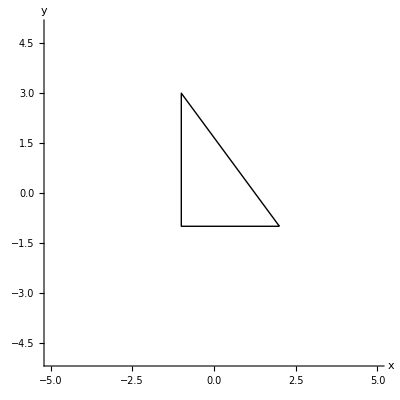

```mathematica
Clear[f]
Clear[g]
Clear[c]
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[n],g[n]},{n,0,1,0.1}];
TableForm[Table[{.1*n,f[.1*n],g[.1*n]},{n,0,10}],TableHeadings->{{},{"t","x","y"}}];
c[t_]:={f[t],g[t]};
Manipulate[ListPlot[Table[c[.01*n],{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}];
Manipulate[Show[ParametricPlot[c[t],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[b]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
Graphics[{Thick,Black,Line[{{2,-1},{-1,3},{-1,-1},{2,-1}}]},Axes->True,AspectRatio->1,
PlotRange->{{-5,5},{-5,5}},AxesLabel->{"x","y"}]
```

```mathematica
Manipulate[Show[ParametricPlot[c[t^20],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[b^20]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
```

## Parametric Curves, Part 9 (modeling straight-line motion at a non-constant speed, making use of the Grid and Plot commands in Mathematica to display graphs side-by-side, and a programming technique to reduece mistakes)

```mathematica
Clear[f]
Clear[g]
Clear[c]
f[t_]:=-3t+2;g[t_]:=4t-1;Table[{f[n],g[n]},{n,0,1,0.1}];
TableForm[Table[{.1*n,f[.1*n],g[.1*n]},{n,0,10}],TableHeadings->{{},{"t","x","y"}}];
c[t_]:={f[t],g[t]};
Manipulate[ListPlot[Table[c[.01*n],{n,0,b}],PlotRange->{{-5,5},{-5,5}}, 
AspectRatio->Automatic,AxesLabel->{"x","y"},
PlotStyle->{PointSize[0.02],Red}],{b,0,100,1}];
Manipulate[Show[ParametricPlot[c[t],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[b]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
Graphics[{Thick,Black,Line[{{2,-1},{-1,3},{-1,-1},{2,-1}}]},Axes->True,AspectRatio->1,
PlotRange->{{-5,5},{-5,5}},AxesLabel->{"x","y"}];
```

```mathematica
h[t_]:=t^2;
Manipulate[Show[ParametricPlot[c[h[t]],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[h[b]]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}],{b,.0001,1}]
```

```mathematica
Paraplot[b_]:=Show[ParametricPlot[c[h[t]],{t,0,b},PlotStyle->{Thick,Red}],
ListPlot[{c[h[b]]},PlotStyle->{Black,PointSize[.02]}],
AspectRatio->Automatic,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}, 
AxesLabel->{"x","y"}];
xplot[b_]:=Plot[f[h[t]],{t,0,b},PlotRange->{{-1,2},{-1,2}},PlotStyle->{Thick, Blue},AxesLabel->{"t","x"}]
yplot[b_]:=Plot[g[h[t]],{t,0,b},PlotRange->{{-1,2},{-1,3}},PlotStyle->{Thick, Blue},AxesLabel->{"t","y"}]
```

```mathematica
Manipulate[Grid[{{Paraplot[b],yplot[b]},{xplot[b],}}],{b,.0001,1}]
```